```mathematica
Guy F. Mongelli, F.E.                                                             ECHE 462
Prof. Sankaran                                                                              3/24/2013
```

```mathematica
Group Assignment #3
```

```mathematica
Problem #3
```

```mathematica
From the solution to the problems 1 and 2, which were performed in Excel by my group members:
```

```mathematica
kimp=((A/10^8)/(V/10^12))(2.65*2*10^-5)/(MWSi*(.2*1.0625/MWHF)^α)
```

0.355212

```mathematica
α=1.6737;
```

```mathematica
In problem 3, the initial concentration is given as:
```

```mathematica
per0=20;
```

```mathematica
The area of a single etch is 10^7 microns (=10meter)in length multiplied by 10 mircons wide.  There is an additional factor of 2 for both sides of the wafer and a factor of 1000 for the number of wafers.
```

```mathematica
A=10^7*10*2*1000 (*microns^2*);
```

```mathematica
A/10^8 (*cm^2)
```

2000

```mathematica
The volume is simply the area associated with the above process multiplied by the 50 micron depth.
```

```mathematica
V=A*50(*microns*);
```

```mathematica
A/V
```

1/50

```mathematica
A/V/MWSi
```

1/3000

```mathematica
The molecular weight of the SiO2 and HF are given:
```

```mathematica
MWSi=60(*g/m0l*);
```

```mathematica
MWHF=20(*g/mol*);
```

```mathematica
The density is corrected as an average of the densities of pute water (assumed 1g/mL ) and pure HF (assumed 1.15 g/mL).
```

```mathematica
rho[x_]=x*1.15+(1-x)1;
```

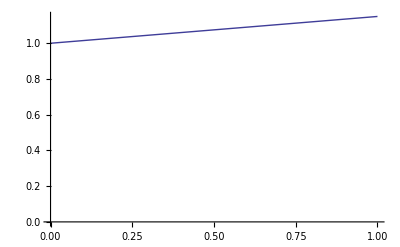

```mathematica
Plot[rho[x],{x,0,1},PlotRange->{0,1.15}]
```

```mathematica
kavg
```

0.552899

```mathematica
It is much easier to solve this problem as a concentration problem. In other words, the initial concentration of HF is known and the concentration when the etch is completed is known from the stoichiometry of the reaction.  Therefore the kinetics can be simplified without inter-relating the density and etch depth as a function of initial and present weight percent then back correlating those functions into time.
```

```mathematica
DSolve[{1/V A/MWSi δ'[per]==-kavg*(per[t]*rho[20]/100/MWHF)^α,δ[0]==0},δ[per],per]
```

{{δ[per]→-0.0188533 per^2.6737}}

```mathematica
DSolve[{1/V A/MWSi δ'[t]==-kavg*(c[t])^α,δ[0]==0},δ[t],t]
```

{{δ[t]→-∫_1^0 -1658.7 c[K[1]]^1.6737ⅆK[1]+∫_1^t -1658.7 c[K[1]]^1.6737ⅆK[1]}}

```mathematica
DSolve[{1/V A/MWSi c'[t]==-kavg*(c[t])^α,c[0]==(5*20)/500},c[t],t]
```

{{c[t]→3.07221/((0.00688093+1. t) (8.20531×10^6+1.19247×10^9 t)^(3263/6737))}}

```mathematica
Clear[c[t]]
```

Clear::ssym: c[t] is not a symbol or a string.

```mathematica
Initial concentration(*in g/ *):
```

```mathematica
.20*1.0625/MWHF
```

0.010625

```mathematica
Final concentration(*in g/mL):
```

```mathematica
(4.85-2.65)/500
```

0.0044

```mathematica
DSolve[{c'[t]==-kimp*(c[t])^α,c[0]==(.20)*1.0625/MWHF},c[t],t]
```

{{c[t]→60926.2/((89.2705+1. t) (8.44163×10^9+9.45625×10^7 t)^(3263/6737))}}

```mathematica
c3[t_]=60926.21755645305/((89.27046078962954+1. t) (8.441633574166765*^9+9.4562451*^7 t)^(3263/6737));
```

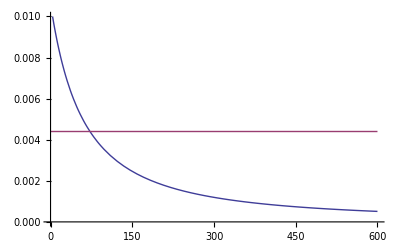

```mathematica
Plot[{c3[t],.0044},{t,0,600},PlotRange->{0,.01}]
```

```mathematica
c3[70]
```

0.00449909

```mathematica
DSolve[{A/V c'[t]==-kavg*(c[t])^α,c[0]==(5*20)/500},c[t],t]
```

{{c[t]→257.179/((0.158787+1. t) (1.17359×10^8+7.39099×10^8 t)^(3263/6737))}}

```mathematica
c2[t_]=257.17886684149283/((0.15878661914732922+1. t) (1.1735905953040347*^8+7.39099177*^8 t)^(3263/6737))
```

257.179/((0.158787+1. t) (1.17359×10^8+7.39099×10^8 t)^(3263/6737))

```mathematica
c2[.115]
```

0.0890918

```mathematica
In seconds:
```

```mathematica
.115*60
```

6.9

```mathematica
c6[t_]=3.07221262633156/((0.006880929695092788+1. t) (8.205307153372029*^6+1.192470715*^9 t)^(3263/6737))
```

3.07221/((0.00688093+1. t) (8.20531×10^6+1.19247×10^9 t)^(3263/6737))

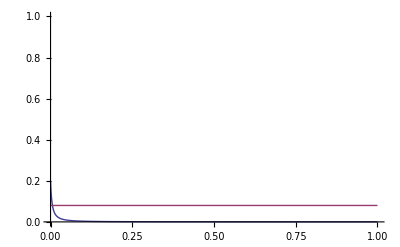

```mathematica
Plot[{c6[t],.08},{t,0,1},PlotRange->{0,1}]
```

```mathematica
c6[100]
```

1.32629×10^-7

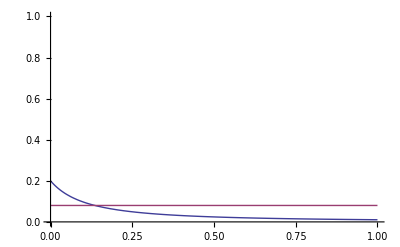

```mathematica
Plot[{c2[t],.08},{t,0,1},PlotRange->{0,1}]
```

```mathematica
c[t_]=0.984327086476161/((0.002646443652454353+1. t) (5.627434589317255*^6+2.126413908*^9 t)^(3263/6737))
```

0.984327/((0.00264644+1. t) (5.62743×10^6+2.12641×10^9 t)^(3263/6737))

```mathematica
(5*20)/500
```

1/5

```mathematica
c[0]
```

0.2

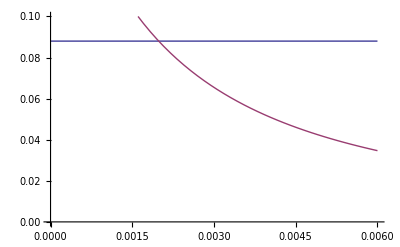

```mathematica
Plot[{.088,0.984/((0.0026+1.t) (5.627*^6+2.126*^9 t)^(3263/6737))},{t,0,.006},PlotRange->{0,.1}]
```

```mathematica
The time until this happens , in minutes,is:
```

```mathematica
c[.0019]
```

0.089577

```mathematica
Solve[0.984/((0.0026+1.t) (5.627*^6+2.126*^9 t)^(3263/6737))==.088,t]
```

$Aborted

```mathematica
Cfinal=(4.85-2.65)*20/500
```

0.088

```mathematica
100/rho[.20]/(MWHF)
```

4.85437

```mathematica
FullSimplify[(20. (1. (1.+0.1499999999999999 per)^1.6737+0.0000926169164323948 per^1.0000000000000002 ((1.+0.1499999999999999 per) per)^1.6737 Hypergeometric2F1[-1.6737,2.6737,3.6737,-0.1499999999999999 per]))/(1.+0.1499999999999999 per)^1.6737]
```

20.+1/(1.+0.15 per)^1.6737 0.00185234 per^1. ((1.+0.15 per) per)^1.6737 Hypergeometric2F1[-1.6737,2.6737,3.6737,-0.15 per]

```mathematica
Delta[per_]=(20. (1. (1.+0.1499999999999999 per)^1.6737+0.0000926169164323948 per^1.0000000000000002 ((1.+0.1499999999999999 per) per)^1.6737 Hypergeometric2F1[-1.6737,2.6737,3.6737,-0.1499999999999999 per]))/(1.+0.1499999999999999 per)^1.6737
```

1/(1.+0.15 per)^1.6737 20. (1. (1.+0.15 per)^1.6737+0.0000926169 per^1. ((1.+0.15 per) per)^1.6737 Hypergeometric2F1[-1.6737,2.6737,3.6737,-0.15 per])

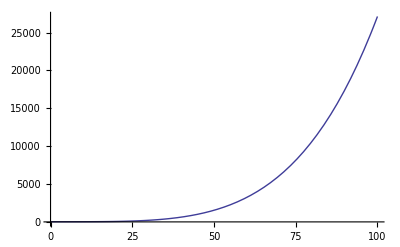

```mathematica
Plot[Delta[per],{per,0,100}]
```